```mathematica
Efield = 
E^(I k Cos[θ1/2]x + I d1)Cos[k Sin[θ1/2]y]+
E^(I k Cos[θ2/2]x+ I d2)Cos[k Sin[θ2/2]z ] + 
E^(I k Cos[θ3/2]z+ I d3)Cos[k Sin[θ3/2]x ];
```

```mathematica
intensity = FullSimplify@ExpToTrig[ComplexExpand[Conjugate[Efield]]*Efield]
```

Cos[d1+k x Cos[θ1/2]]^2 Cos[k y Sin[θ1/2]]^2+Cos[d2+k x Cos[θ2/2]]^2 Cos[k z Sin[θ2/2]]^2+2 Cos[d2+k x Cos[θ2/2]] Cos[d3+k z Cos[θ3/2]] Cos[k z Sin[θ2/2]] Cos[k x Sin[θ3/2]]+2 Cos[d1+k x Cos[θ1/2]] Cos[k y Sin[θ1/2]] (Cos[d2+k x Cos[θ2/2]] Cos[k z Sin[θ2/2]]+Cos[d3+k z Cos[θ3/2]] Cos[k x Sin[θ3/2]])+(Cos[k y Sin[θ1/2]] Sin[d1+k x Cos[θ1/2]]+Cos[k z Sin[θ2/2]] Sin[d2+k x Cos[θ2/2]])^2+Cos[k x Sin[θ3/2]] (Cos[k x Sin[θ3/2]]+2 (Cos[k y Sin[θ1/2]] Sin[d1+k x Cos[θ1/2]]+Cos[k z Sin[θ2/2]] Sin[d2+k x Cos[θ2/2]]) Sin[d3+k z Cos[θ3/2]])

```mathematica
FullSimplify[intensity/.{z->0}]
intensity/.{x->0};
intensity/.{y->0};
```

1/2 (4+4 Cos[k x (Cos[θ1/2]-Cos[θ2/2])] Cos[k y Sin[θ1/2]]+Cos[2 k y Sin[θ1/2]]+4 (Cos[k x Cos[θ2/2]]+Cos[k x Cos[θ1/2]] Cos[k y Sin[θ1/2]]) Cos[k x Sin[θ3/2]]+Cos[2 k x Sin[θ3/2]])

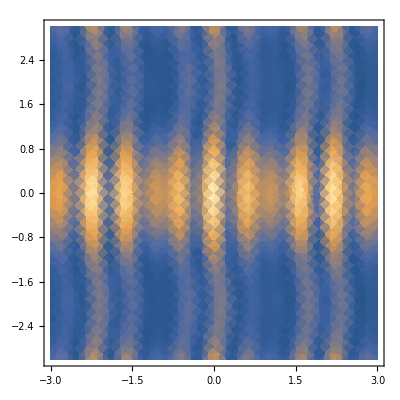

```mathematica
DensityPlot[intensity/.{z->0}/.{k->10,θ1->0.1π,θ2->0.1π,θ3->0.1π,d1->0.5,d2->0,d3->0.0},{x,-3,3},{y,-3,3}]
```

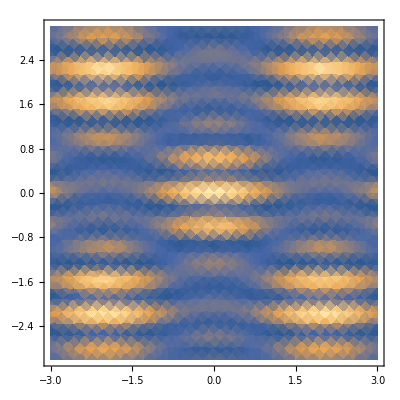

```mathematica
DensityPlot[intensity/.{x->0}/.{k->10,θ1->0.1π,θ2->0.1π,θ3->0.1π,d1->0.1,d2->0.5,d3->0.0},{y,-3,3},{z,-3,3}]
```

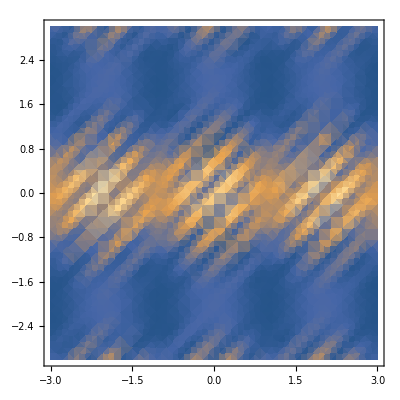

```mathematica
DensityPlot[intensity/.{y->0}/.{k->10,θ1->0.1π,θ2->0.1π,θ3->0.1π,d1->0.0,d2->0.0,d3->0.9},{x,-3,3},{z,-3,3}]
```

```mathematica
Solve[αGR IR + αGB IB == αRRP IR β+ αRBP IB β+αRRS IR + αRBS IB/.{IR-> γ IB},γ]//FullSimplify
```

{{γ→(-αGB+αRBS+αRBP β)/(αGR-αRRS-αRRP β)}}

```mathematica
(γ αGR + αGB)/.{γ->(-αGB+αRBS+αRBP β)/(αGR-αRRS-αRRP β)}//Together
```

(αGR αRBS-αGB αRRS+αGR αRBP β-αGB αRRP β)/(αGR-αRRS-αRRP β)

```mathematica
αRB ==αRBS+αRBP β
αRR== αRRS+αRRP β
```

```mathematica
(γ αGR + αGB)/.{γ->(-αGB+αRB)/(αGR-αRR)}//Together
```

(αGR αRB-αGB αRR)/(αGR-αRR)